```mathematica
epsilon = 0.08; d = 0.7; c = 0.8; ff[v_]:=v-v^3/3;
```

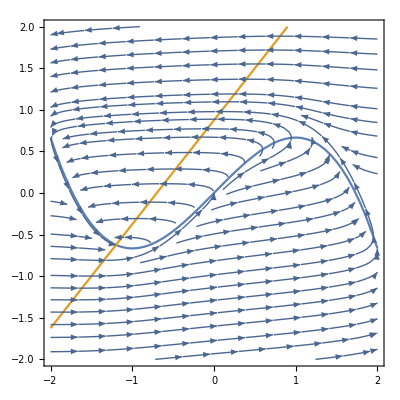

```mathematica
II = 0; (*Part A*)
Show[ContourPlot[{v-v^3/3-w+II==0,epsilon*(v + d- c*w)==0},{v,-2,2},{w,-2,2}],StreamPlot[{v-v^3/3-w+II,epsilon*(v + d- c*w)},{v,-2,2},{w,-2,2}]]
```

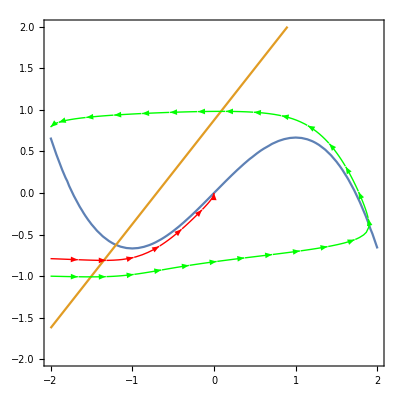

```mathematica
Show[ContourPlot[{v-v^3/3-w+II==0,epsilon*(v + d- c*w)==0},{v,-2,2},{w,-2,2}],StreamPlot[{v-v^3/3-w+II,epsilon*(v + d- c*w)},{v,-2,2},{w,-2,2},StreamPoints->{{  {  {0,0} , Red }  ,    {  {-2,-1} , Green  }  }  }] ]
```

```mathematica
points= Join[Table[{v,v-v^3/3+II},{v,-2,2,0.2}],Table[{c*w-d,w},{w,-2,2,0.2}]];
```

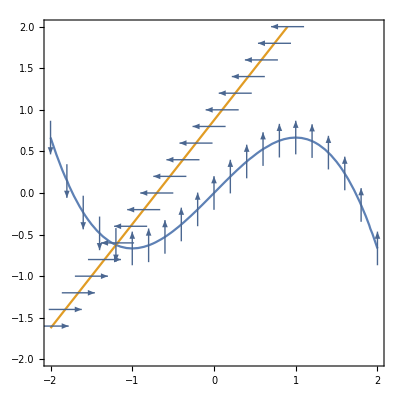

```mathematica
Show[ContourPlot[{v-v^3/3-w+II==0,epsilon*(v + d- c*w)==0},{v,-2,2},{w,-2,2}],VectorPlot[{(v-v^3/3-w+II)/Sqrt[(v-v^3/3-w+II)^2+(epsilon*(v + d- c*w))^2],(epsilon*(v + d- c*w))/Sqrt[(v-v^3/3-w+II)^2+(epsilon*(v + d- c*w))^2]},{v,-2,2},{w,-2,2},VectorPoints->points]]
```

0.3

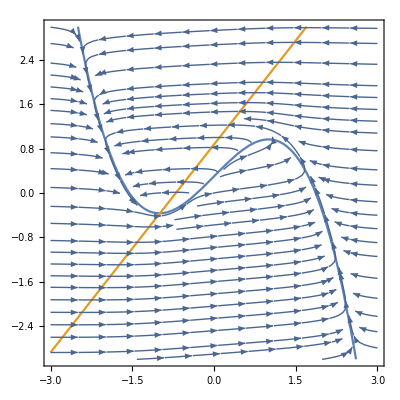

```mathematica
II2 = 0.3  (*Part B*)
Show[ContourPlot[{v-v^3/3-w+II2==0,epsilon*(v + d- c*w)==0},{v,-3,3},{w,-3,3}],StreamPlot[{v-v^3/3-w+II2,epsilon*(v + d- c*w)},{v,-3,3},{w,-3,3}]]
```